```mathematica
SetDirectory[SystemDialogInput["Directory"]]
```

D:\grafiliv - stayin alive 2

```mathematica
SetDirectory["D:\\grafiliv - stayin alive 2\\"]
```

D:\grafiliv - stayin alive 2

```mathematica
GetOrg[orgNo_]:=Module[{path1,path2,birth,death},
path1 = StringForm["organisms\\org``.json",orgNo]//ToString;
path2 = StringForm["orgDeaths\\org``.json",orgNo]//ToString;
birth=Import[path1];
death=Import[path2];
{
"step"/.birth,
"step"/.death,
"cause"/.death
}
]
GetOrgLifespan[orgNo_]:=Module[{birth,death,cause},
{birth,death,cause}=GetOrg[orgNo];
{birth,death}
]
```

```mathematica
PackOrgTimelines[ts_]:=Module[{rows,org,i,timelines},
timelines=ts;
rows={};
While[Length[timelines]>0,
org=First[timelines];
timelines=Rest[timelines];
i=0;
While[i≤ Length[rows],
If[Depth[rows⟦i⟧]==2,rows⟦i⟧={rows⟦i⟧}];
If[Min[org]>Max[rows⟦i⟧],
AppendTo[rows⟦i⟧,org];
Break[];
];
i++
];
If[i> Length[rows],
AppendTo[rows,org];
];
];
Map[Interval,rows,{-2}]
]
```

```mathematica
LastNOrgs[n_]:=Take[Sort[FromDigits/@deadOrganisms],-n]
```

```mathematica
deadOrganisms=
StringCases[
FileNames["*","orgDeaths"],
"orgDeaths\\org"~~i:DigitCharacter..~~".json"-> i
]//Flatten;
nDead=deadOrganisms//Length
```

349884

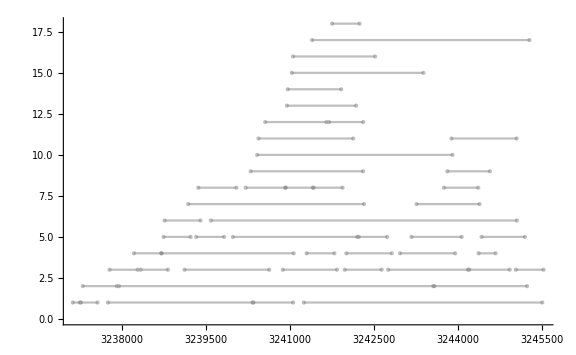

```mathematica
orgs=Map[GetOrgLifespan,LastNOrgs[50]];
timelines=PackOrgTimelines[orgs];
NumberLinePlot[timelines,ImageSize->Large,PlotStyle->Directive[Opacity[0.5],Gray]]
```